# Running Coupling

```mathematica
ClearAll["Global`*"]
```

```mathematica
myTicks[lower_,upper_,step_]:=Flatten[Module[{Local=#,LocalTicks},LocalTicks=Log[10,Range[10^(#-1),10^#,(10^#-10^(#-1))/(10-1)]];
Join[{#,""}&/@Most[LocalTicks],{{Last[LocalTicks],Which[Last[LocalTicks]==0,1,Last[LocalTicks]==1,10,True,Power[10,ToString[Last[LocalTicks]]]],{0.03,0}(*longer ticks*)}}]]&/@Range[lower,upper,step],1];
```

## SM parameters

```mathematica
sw = √0.23116;
cw = √(1 - sw^2);
mZ = 91.1876; 
mW = 80.399;
(*mtpole = 173.1-0.7*2.5;*)
GF = 1.16637 10^-5;
v=1/(√(√2*GF));
mb=4.19;mc=1.27;ms=0.1;
α0=1/137.035999679;
ΔαhmZ=0.02758;
αmZ= α0/(1-0.03150-ΔαhmZ+0.00007);
αsmZ=0.1181+0.0011*(1);

Mpl=2.4*10^18;(*Planck mass*)
mhpole=125.18+0.16*(0);

ye=2.8*10^-6;
yμ=5.9*10^-4;
yτ=1.0*10^-2;
yd=1.6*10^-5/2;
ys=3.1*10^-4/2;
yb=1.6*10^-2/2;
yu=7.4*10^-6/2;
yc=3.6*10^-3/2;
κ=1/(16 π^2)(*Phase space factor*);
Nf=6;(*number of flavor why?*)
Ng=3;(*number of generation*)
z3=Zeta[3];
(*QCD*)
CA=3;(*Casimir operator Subscript[C, A]=Subscript[C, 2](adj)*)
CF=4/3;(*Casimir operator Subscript[C, F]=Subscript[C, 2](fund)*)
TR=1/2;(*Index Subscript[T, R](fund)*)
dR=3;(*dimension of representation, can be understood as color factor*)
SmoothUnitStep[x_]:=ArcTan[10x]/π+1/2;
g1mZ=(√(4π αmZ))/cw;
g2mZ=(√(4π αmZ))/sw;
g3mZ=√(4π*αsmZ);
αsmZ=0.1179;

(*Measured pole masses*)
mhpole=125.10;
mtpole=172.76;

(*MSbar couplings*)
λmtpole:=0.12604+0.00206*(mhpole-125.15)-0.00004(mtpole-173.34);
ytmtpole:=0.93690+0.00556(mtpole-173.34)-0.00003(mhpole-125.15)-0.00042((αsmZ-0.1184)/0.0007);
g3mtpole=1.1666+0.00314((αsmZ-0.1184)/0.0007)-0.00046(mtpole-173.34);
g2mtpole=0.64779+0.00004(mtpole-173.34)+0.00011*(mW-80.384)/0.014;
g1mtpole=0.35830+0.00011(mtpole-173.34)-0.00020*(mW-80.384)/0.014;
```

## 1TeV scale Extra Fermion

```mathematica
βyt[λ_,yt_,g3_,g2_,g1_,yN_]:=2yt(κ yt^2(3/4+1/2 dR)+κ g3^2(-3CF)+3 κ^2 λ^2+(-6)κ^2 yt^2 λ+κ^2 yt^4(3/4-9/4 dR)+κ^2 g3^2 yt^2(6CF+5/2 CF dR)+κ^2 g3^4(-3/2 CF^2-97/6 CA CF+10/3 Nf TR CF)+κ^3 λ^3(-18)+κ^3 yt^2 λ^2(285/8-45/4 dR)+κ^3 yt^4 λ(63/2+45/2 dR)+κ^3 yt^6(-345/32+107/32 dR+39/16 dR^2+9/4 z3+3/2 z3 dR)+κ^3 g3^2 yt^2 λ(6CF)+κ^3 g3^2 yt^4(-57/2 CF-81/8 CF dR)+κ^3 g3^4 yt^2(471/16 CF^2-119/8 CF^2 dR+25TR CF+717/16 CA CF+77/4 CA CF dR-33/4 Nf TR CF-4Nf TR CF dR-27z3 CF^2+18z3 CF^2 dR-27/2 z3 CA CF-9 z3 CA CF dR)+κ^3 g3^6(-129/2 CF^3+129/4 CA CF^2-11413/108 CA^2 CF+46Nf TR CF^2+556/27 Nf CA TR CF+140/27 Nf^2 TR^2 CF-48z3 Nf TR CF^2+48z3 Nf CA TR CF))+
yt κ(-9/4 g2^2-17/12 g1^2)+
yt κ^2(5/2 yt^2(17/12 g1^2+9/4 g2^2)+yt^2(223/48 g1^2+135/16 g2^2)+25/9 g1^4(9/200+29/45 Ng)+58/57 g1^4*2-3/4 g1^2 g2^2+19/9 g1^2 g3^2-(35/4-Ng)g2^4+9 g2^2 g3^2);
βg3[λ_,yt_,g3_,g2_,g1_,yN_]:=2g3(κ g3^2(-11/6 CA+2/3 Nf TR)+κ^2 g3^2 yt^2(-2TR)+κ^2 g3^4(-17/3 CA^2+2Nf TR CF+10/3 Nf CA TR)+κ^3 g3^2 yt^4(9/2 TR+7/2 TR dR)+κ^3 g3^4 yt^2(-3TR CF-12CA TR)+κ^3 g3^6(-2857/108 CA^3-Nf TR CF^2+205/18 Nf CA TR CF+1415/54 Nf CA^2 TR-22/9 Nf^2 TR^2 CF-79/27 Nf^2 CA TR^2))+g3^3 κ^2(11/6 g1^2+9/2 g2^2);
βg1[λ_,yt_,g3_,g2_,g1_,yN_]:=-g1^3 κ(-1/6-20/9 Ng+2/3*2)+g1^3 κ^2 5/3(199/30 g1^2+6/5*2 g1^2+27/10 g2^2+44/5 g3^2-17/10 yt^2);
βg2[λ_,yt_,g3_,g2_,g1_,yN_]:=-g2^3 κ(43/6-4/3 Ng)+g2^3 κ^2(3/2 g1^2+35/6 g2^2+12 g3^2-3/2 yt^2);
βλ[λ_,yt_,g3_,g2_,g1_,t_,yN_]:=2(12κ λ^2+2κ yt^2 λ dR+κ yt^4(-dR)+κ (yN SmoothUnitStep[t-Log[1000/mZ]])^4(-4)+2κ (yN SmoothUnitStep[t-Log[1000/mZ]])^2 λ 2+κ^2 λ^3(-156)+κ^2 yt^2 λ^2(-24dR)+κ^2 yt^4 λ(-1/2 dR)+κ^2 yt^6(5dR)+κ^2 g3^2 yt^2 λ(10CF dR)+κ^2 g3^2 yt^4(-4CF dR)+κ^3 λ^4(3588+2016z3)+κ^3 yt^2 λ^3(291dR)+κ^3 yt^4 λ^2(789/2 dR-36 dR^2+252z3 dR)+κ^3 yt^6 λ(-1881/8 dR+80 dR^2-66z3 dR)+κ^3 yt^8(13/2 dR-195/8 dR^2-12z3 dR)+κ^3 g3^2 yt^2 λ^2(-306CF dR+288z3 CF dR)+κ^3 g3^2 yt^4 λ(895/4 CF dR-324 z3 CF dR)+κ^3 g3^2 yt^6(-19/2 CF dR+60z3 CF dR)+κ^3 g3^2 yt^2 λ(-119/2 CF^2 dR+77CA CF dR-16Nf TR CF dR+72z3 CF^2 dR-36z3 CA CF dR)+κ^3 g3^4 yt^4(131/2 CF^2 dR+48TR CF dR-109/2 CA CF dR+10Nf TR CF dR-48z3 CF^2 dR+24z3 CA CF dR))+κ/2(-(3 g1^2+9 g2^2)2λ+9/4(1/3 g1^4+2/3 g1^2 g2^2+g2^4))+κ^2/2((54 g2^2+18 g1^2)4 λ^2-((313/8-10Ng)g2^4-39/4 g2^2 g1^2-(687/200+2Ng)25/9 g1^4+60/19*2 g1^4)2λ+(497/8-8Ng)g2^6-(97/40+8/5 Ng)5/3 g2^4 g1^2-(717/200+8/5 Ng)25/9 g2^2 g1^4-(531/1000+24/25 Ng)125/27 g1^6-1728/505*2 g1^6-8/3 g1^2 2 yt^4-9/2 g2^4 yt^2+5/3 g1^2(63/5 g2^2-57/10 g1^2)yt^2+10 *2 λ yt^2(17/12 g1^2+9/4 g2^2));
```

```mathematica
list1TeV={};
```

## v_R=10^5 GeV

```mathematica
vR=10^5;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
gX=√((g2[vR]^2 g1[vR]^2)/(g2[vR]^2-g1[vR]^2));
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+gX^2)vR^2;
λvR=λ[vR],
EE=1/(6π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
strength=2EE/λvR
}
,{yN,0.6,0.8,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.7}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.7}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
gX=√((g2[vR]^2 g1[vR]^2)/(g2[vR]^2-g1[vR]^2));
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+gX^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-16 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

0.701668

0.677151

```mathematica
tab={};
For[i=2,i<7,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -15.1996 and x = -15.1996.

{{1.×10^6,937.209,201.406},{3.16228×10^6,617.699,99.0085},{1.×10^7,444.672,62.6064},{3.16228×10^7,337.263,41.5812},{1.×10^8,267.69,28.6874}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,7}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list1TeV,{5,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{431.231}

7.05079

1.13407×10^7

113.407

## v_R=10^5.5 GeV

```mathematica
vR=10^5.5;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
gX=√((g2[vR]^2 g1[vR]^2)/(g2[vR]^2-g1[vR]^2));
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+gX^2)vR^2;
λvR=λ[vR],
EE=1/(6π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
strength=2EE/λvR
}
,{yN,0.5,0.7,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.6}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.6}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
gX=√((g2[vR]^2 g1[vR]^2)/(g2[vR]^2-g1[vR]^2));
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+gX^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-16 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

0.633204

0.587903

```mathematica
tab={};
For[i=3,i<10,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -15.6496 and x = -15.6496.

{{1.×10^7,1243.01,282.474},{3.16228×10^7,780.887,131.006},{1.×10^8,559.649,77.1173},{3.16228×10^8,430.856,50.1898},{1.×10^9,348.224,34.8782},{3.16228×10^9,291.459,25.4953},{1.×10^10,250.343,19.401}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,8}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list1TeV,{5.5,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{435.836}

8.47489

2.98781×10^8

944.827

## v_R=10^6 GeV

```mathematica
vR=10^6;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
gX=√((g2[vR]^2 g1[vR]^2)/(g2[vR]^2-g1[vR]^2));
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+gX^2)vR^2;
λvR=λ[vR],
EE=1/(6π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
strength=2EE/λvR
}
,{yN,0.45,0.65,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.5}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.5}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
gX=√((g2[vR]^2 g1[vR]^2)/(g2[vR]^2-g1[vR]^2));
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+gX^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-16 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

0.577431

0.525244

```mathematica
tab={};
For[i=4,i<11,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -15.5224 and x = -15.5224.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -20.6253 and x = -20.6253.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -21.342 and x = -21.342.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

{{1.×10^8,1197.31,225.978},{3.16228×10^8,819.411,121.84},{1.×10^9,616.237,75.982},{3.16228×10^9,491.055,51.507},{1.×10^10,407.131,37.0401},{3.16228×10^10,347.329,27.8589},{1.×10^11,302.696,21.6999}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,10}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list1TeV,{6,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{440.442}

9.77773

5.99518×10^9

5995.18

## v_R=10^6.5 GeV

```mathematica
vR=10^6.5;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
gX=√((g2[vR]^2 g1[vR]^2)/(g2[vR]^2-g1[vR]^2));
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+gX^2)vR^2;
λvR=λ[vR],
EE=1/(6π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
strength=2EE/λvR
}
,{yN,0.4,0.6,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.5}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.5}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
gX=√((g2[vR]^2 g1[vR]^2)/(g2[vR]^2-g1[vR]^2));
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+gX^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-16 mNsq^2);
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

0.529737

0.470585

```mathematica
tab={};
For[i=5,i<12,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -20.8231 and x = -20.8231.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -20.3801 and x = -20.3801.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -21.6862 and x = -21.6862.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

{{1.×10^9,1185.01,191.795},{3.16228×10^9,865.781,113.678},{1.×10^10,678.38,74.8541},{3.16228×10^10,556.273,52.8255},{1.×10^11,470.89,39.2074},{3.16228×10^11,408.016,30.238},{1.×10^12,359.858,24.0304}}

```mathematica
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,11}]
escapefinal=10^escape+vR
escapefinal/vR
AppendTo[list1TeV,{6.5,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{445.047}

11.1879

1.54122×10^11

48737.8

## v_R=10^7GeV = 10^4 TeV

```mathematica
vR=10^7;
list=Table[{
yN,
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
gX=√((g2[vR]^2 g1[vR]^2)/(g2[vR]^2-g1[vR]^2));
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+gX^2)vR^2;
λvR=λ[vR],
EE=1/(6π vR^3)(2 mWsq^(3/2)+mZsq^(3/2));
strength=2EE/λvR
}
,{yN,0.35,0.55,0.02}];
runninglist={#1,#2}&@@@list;
running[yN_]:=Interpolation[runninglist][yN]
Yukawaupper=x/.FindRoot[running[x],{x,0.4}]
PTstrengthlist={#1,#3}&@@@ Select[list,#[[2]]>0 &];
strengthfunc[yN_]:=Interpolation[PTstrengthlist][yN];
Yukawalower=x/.FindRoot[strengthfunc[x]-1.0,{x,0.4}]
yN=Yukawalower;
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t,yN],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],yN],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s};
gX=√((g2[vR]^2 g1[vR]^2)/(g2[vR]^2-g1[vR]^2));
mtsq=1/2 yt[vR]^2 vR^2;
mNsq=1/2 yN^2 vR^2;
mWsq=1/4 g2[vR]^2 vR^2;
mZsq=1/4(g2[vR]^2+gX^2)vR^2;
λvR=λ[vR];
mHvR=√(2λvR) vR;
B=1/(64 π^2 vR^4)(6 mWsq^2+3 mZsq^2-12 mtsq^2-16 mNsq^2);
vR=10^4;
V0T[ϕ_]:=-1/2 λvR vR^2 ϕ^2+1/4 λvR ϕ^4+2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];DV0T[ϕ_]:=-λvR vR^2 ϕ+λvR ϕ^3+4B vR^2 ϕ-6B ϕ^3+4B ϕ^3 Log[ϕ^2/vR^2]+2B ϕ^3;
Vb[ϕ_]:=V0T[ϕ+vR]-V0T[vR]/;ϕ>=0;
Vb[ϕ_]:=V0T[-ϕ+vR]-V0T[vR]/;ϕ<0;
DVb[ϕ_]:=DV0T[ϕ+vR]/;ϕ>=0;
DVb[ϕ_]:=-DV0T[-ϕ+vR]/;ϕ<0;
dVexp[y_]:=DVb[ⅇ^y];
```

0.487381

0.417361

```mathematica
tab={};
For[i=6,i<14,i++,
ϕi=10^(0.5*i)vR;
rf=1/ϕi*10^3;
riuder=1/ϕi*10^-3;
riover=1/ϕi*10^1;
For[j=0,j<50,j++,
ri=(riuder+riover)/2;
flago=0;
expsol=NDSolve[{ⅇ^(y[x]-2x)(y''[x]+y'[x]^2+2y'[x])-dVexp[y[x]]==0,y[Log[ri]]==Log[ϕi],y'[Log[ri]]==0,WhenEvent[{y[x]≤0},{flago=1;"StopIntegration"}]},y,{x,Log[ri],Log[rf]}];
ysol[r_]:=(y[r]/.expsol)[[1]];
If[flago==1,riover=ri,riuder=ri];
];
ϕsol[r_]:=Exp[ysol[Log[r]]];
S=2 π^2 1/4 ri^4(Vb[ϕi])+2 π^2 NIntegrate[(Vb[ϕsol[r]]+1/2 ϕsol'[r]^2)r^3,{r,ri,rf}];
λeff=-4 Vb[ϕi]/ϕi^4;
Sdiff=S-8 π^2/(3λeff);
AppendTo[tab,{ϕi,S,Sdiff}]
]
tab(*Here the escape point unit should be TeV!*)
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between x = -20.4751 and x = -20.4751.

{{1.×10^7,1242.65,177.616},{3.16228×10^7,949.634,112.119},{1.×10^8,766.452,77.0339},{3.16228×10^8,641.745,56.1233},{1.×10^9,551.625,42.6959},{3.16228×10^9,483.555,33.5753},{1.×10^10,430.364,27.1015},{3.16228×10^10,387.674,22.3411}}

```mathematica
vR=10^7;(*Back to GeV*)
H0=71  1/(3.089*10^19)*6.58*10^-25 (*Unit GeV*)
{Sbound}=SE/.Solve[vR^4 Exp[-SE]==H0^4,SE]
actionlist={Log10[#1],#2}&@@@tab;
Sfunc[logϕ_]:=Interpolation[actionlist][logϕ];
escape=logϕ/.FindRoot[Sfunc[logϕ]==Sbound,{logϕ,10}]
escapefinal=10^(escape+3)+vR
escapefinal/vR
AppendTo[list1TeV,{7,escapefinal/vR}];
```

1.5124×10^-42

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{449.652}

9.80467

6.37786×10^12

637786.

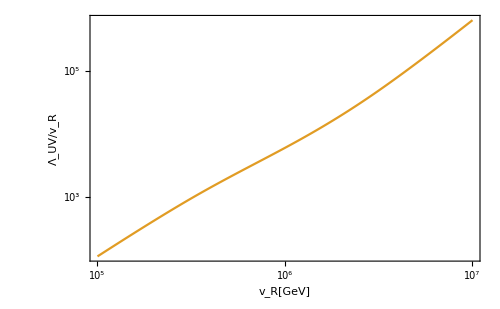

```mathematica
plot1TeV=ListLinePlot[{#1,Log10[#2]}&@@@list1TeV,InterpolationOrder->3,BaseStyle->{FontSize->24,FontFamily->"Times"},Frame->True,FrameLabel->{Style["v_R[GeV]",FontFamily->"Times",FontSize->24],Style["Λ_UV/v_R",FontFamily->"Times",FontSize->24]},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,FrameTicks->{{myTicks[-1,6,1],None},{myTicks[4,8,1],None}},PlotStyle->ColorData[97,2],PlotRange->{{5,7},Automatic}]
```